# ChiSquareRandomnessTest

Tests a sequence of 0s and 1s or a set of random reals between 0 and 1 for equidistribution and returns a p-value

## DefinitionDefinitionDefine your function using the name you gave in the Title line above. You can add input cells and extra code to define additional input cases or prerequisites. All definitions, including dependencies, will be included in the generated resource function. This section should be evaluated before creating the Examples section below.

Equidistribution tests

Chi square test for independence — sequences of 0s and 1s

```mathematica
chiSquareTest01[seq_]:=<|"TestStatistic"->(#2-2#1)^2/#2,"PValue"-> 1.-CDF[ChiSquareDistribution[1],(#2-2#1)^2/#2],"DegreesofFreedom"->1|>&[Total[seq],Length[seq]]
ChiSquareRandomnessTest[seq_List/;VectorQ[seq,#==0||#==1&]]:=chiSquareTest01[seq]["PValue"];
ChiSquareRandomnessTest[seq_List/;VectorQ[seq,#==0||#==1&],"PValue"]:=chiSquareTest01[seq]["PValue"];
ChiSquareRandomnessTest[seq_List/;VectorQ[seq,#==0||#==1&],"TestStatistic"]:=chiSquareTest01[seq]["TestStatistic"];
```

Chi square test for independence — random reals between 0 and 1

```mathematica
chiSquareTestRandomReal[seq_]:=Module[{stat=Total[(BinCounts[seq,1/Length[seq]]-1)^2]},
<|"TestStatistic"->stat,"PValue"->1.-CDF[ChiSquareDistribution[Length[seq]-2],stat],"DegreesofFreedom"->Length[seq]-2|>
];
ChiSquareRandomnessTest[seq_List/;VectorQ[seq,IntervalMemberQ[Interval[{0,1}],#]&&InexactNumberQ[#]&]]:=chiSquareTestRandomReal[seq]["PValue"];
ChiSquareRandomnessTest[seq_List/;VectorQ[seq,IntervalMemberQ[Interval[{0,1}],#]&&InexactNumberQ[#]&],req_String/;MemberQ[{"TestStatistic","PValue"},req]]:=chiSquareTestRandomReal[seq][req];
```

## Documentation

### UsageUsageDocument input usage cases by first typing an input structure, then pressing to add a brief explanation of the function’s behavior for that structure. Pressing repeatedly will create new cases as needed. Every input usage case defined above should be demonstrated explicitly here. See existing documentation pages for examples.

ChiSquareRandomnessTest[sequence]

tests a sequence of 0s and 1s and returns a p-value.

ChiSquareRandomnessTest[sequence]

tests a sequence of random reals between 0 and 1 and returns a p-value.

ChiSquareRandomnessTest[sequence,"property"]

tests a sequence of either random reals between 0 and 1 or a sequence of 0s and 1s and returns a a property of the test.

### Details & OptionsDetails & OptionsGive a detailed explanation of how the function is used and configured (e.g. acceptable input types, result formats, options specifications, background information). This section may include multiple cells, bullet lists, tables, hyperlinks and additional styles/structures as needed. Add any other information that may be relevant, such as when the function was first discovered or how and why it is used within a given field. Include all relevant background or contextual information related to the function, its development, and its usage.

Properties include

"TestStatistic" | Returns the chi square test statistic
"PValue" | Returns the p-value associated with the test

The bin size for testing random reals is 1/n where n is the sequence length.

The chi square randomness test works best for larger sequences of numbers.

The chi square randomness test only tests for equidistribution.

## ExamplesExamplesDemonstrate the function’s usage, starting with the most basic use case and describing each example in a preceding text cell. Within a group, individual examples can be delimited by inserting page breaks between them (either using "[Right-click]"" ▶ ""Insert Page Break" between cells or through the menu using "Insert"" ▶ ""Page Break"). Examples should be grouped into Subsection and Subsubsection cells similarly to existing documentation pages. Here are some typical Subsection names and the types of examples they normally contain: "◼ ""Basic Examples: "most basic function usage "◼ ""Scope: "input and display conventions, standard computational attributes (e.g. threading over lists) "◼ ""Options: "available options and parameters for the function "◼ ""Applications: "standard industry or academic applications "◼ ""Properties and Relations: "how the function relates to other functions "◼ ""Possible Issues: "limitations or unexpected behavior a user might experience "◼ ""Neat Examples: "particularly interesting, unconventional, or otherwise unique usage

### Basic Examples

Generate a sequence of random integers and test it for equidistribution:

```mathematica
sequence=RandomInteger[{0,1},1000];
```

Visualize the sequence:

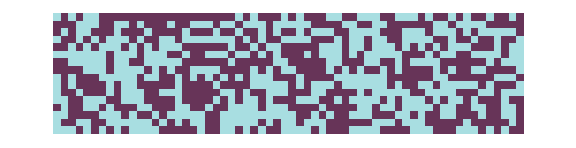

```mathematica
ArrayPlot[Partition[sequence,16]ᵀ,]
```

```mathematica
ChiSquareRandomnessTest[sequence,"TestStatistic"]
```

9/10

```mathematica
ChiSquareRandomnessTest[sequence,"PValue"]
```

0.342782

Generate a sequence of random reals and test it for equidistribution:

```mathematica
sequence=RandomReal[{0,1},1000];
```

Visualize the sequence:

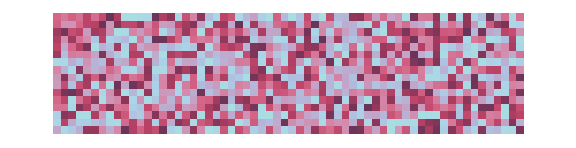

```mathematica
ArrayPlot[Partition[sequence,16]ᵀ,]
```

```mathematica
ChiSquareRandomnessTest[sequence,"TestStatistic"]
```

990

```mathematica
ChiSquareRandomnessTest[sequence,"PValue"]
```

0.565376

Generate variates of the normal distribution and test if they are equidistributed:

```mathematica
variates=RandomVariate[NormalDistribution[],1000];
```

Visualize the variates:

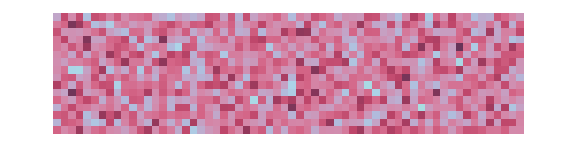

```mathematica
ArrayPlot[Partition[variates,16]ᵀ,]
```

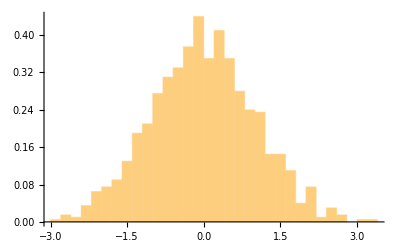

```mathematica
Histogram[variates,40,"PDF"]
```

Transform the variates so that the range is between 0 and 1:

```mathematica
transformedvariates=CDF[NormalDistribution[],variates];
```

Visualize the transformed variates:

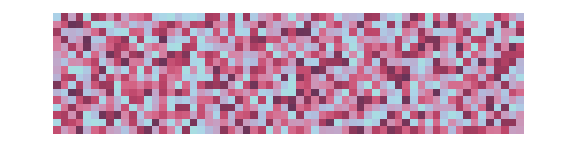

```mathematica
ArrayPlot[Partition[transformedvariates,16]ᵀ,]
```

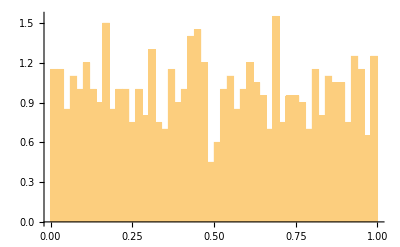

```mathematica
Histogram[transformedvariates,40,"PDF"]
```

Test if the transformed variates are equidistributed:

```mathematica
ChiSquareRandomnessTest[transformedvariates,"TestStatistic"]
```

1057

```mathematica
ChiSquareRandomnessTest[transformedvariates,"PValue"]
```

0.0950488

### Applications

Test to see if rule 30 is equidistributed:

```mathematica
rule30seq=CellularAutomaton[30, {{1}, 0}, {10000,0}]ᵀ⟦1⟧;
```

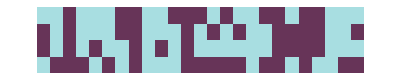

```mathematica
ArrayPlot[Partition[Take[rule30seq,100],25],]
```

```mathematica
ChiSquareRandomnessTest[rule30seq]
```

0.515713

## Source & Additional Information

### Contributed ByContributed ByEnter the name of the person, people or organization that should be publicly credited with contributing this function.

Emmy/Noah Blumenthal
noahb320@gmail.com
emmyb320@bu.edu

### KeywordsKeywordsList relevant terms (e.g. functional areas, algorithm names, related concepts) that should be used to include the function in search results.

Randomness

Statistics

### Categories

Cloud & Deployment |  Core Language & Structure
 Data Manipulation & Analysis |  Engineering Data & Computation
 External Interfaces & Connections |  Financial Data & Computation
 Geographic Data & Computation |  Geometry
 Graphs & Networks |  Higher Mathematical Computation
 Images |  Just For Fun
 Knowledge Representation & Natural Language |  Machine Learning
 Notebook Documents & Presentation |  Programming Utilities
 Repository Tools |  Scientific and Medical Data & Computation
 Social, Cultural & Linguistic Data |  Sound
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Time-Related Computation
 User Interface Construction |  Visualization & Graphics

### Related SymbolsRelated SymbolsList up to twenty documented, system-level Wolfram Language symbols related to the function.

DistributionFitTest

### Related Resource ObjectsRelated Resource ObjectsList the names of published resource objects from any Wolfram repository that are related to this function.

OPERM5RandomnessTest

### Source/Reference CitationSource/Reference CitationGive a bibliographic-style citation for the original source of the function and/or its components (e.g. a published paper, algorithm, or code repository).

Source, reference or citation information

### LinksLinksList additional URLs or hyperlinks for external information related to the function.

### TestsTestsSpecify an optional list of tests for verifying that the function is working properly in any environment. Tests can be specified as Input/Output cell pairs or as symbolic VerificationTest expressions for including additional options.

## Author Notes

The chi square test is meant to work with sequences of a certain length (typically longer than 30).

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.

Additional information for the reviewer.